```mathematica
Salary=Import["/Users/aliak/Desktop/filtered_salary.csv"]
```

```mathematica
JobPosting=Import["/Users/aliak/Desktop/final_job_postings.csv"]
```

```mathematica
(*Visualization of the count of jobs as per the experience level*)
```

```mathematica
experienceLevels= Salary[[All,2]];
```

```mathematica
enCount= Count[experienceLevels, "EN"];
```

```mathematica
miCount= Count[experienceLevels, "MI"];
```

```mathematica
counts= {enCount, miCount};
```

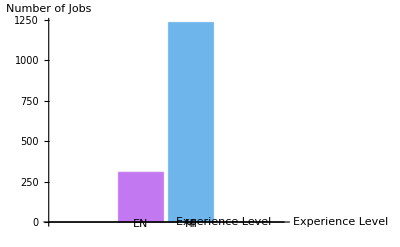

```mathematica
BarChart[counts, ChartLabels->{"EN", "MI"}, ChartStyle->"Pastel", AxesLabel->{"Experience Level", "Number of Jobs"}]
```

```mathematica
(*Finding out the number of employees residing in US and comparing it with employees not residing in US for comparison- remote aspect*)
```

```mathematica
employeeResidenceCol=8;
numberOfEmployeesInUS=Length[Select[Salary,#[[employeeResidenceCol]]==="US"&]];
numberOfEmployeesInUS
```

1511

```mathematica
numberOfEmployeesOther=Length[Salary]-numberOfEmployeesInUS;
```

```mathematica
32
```

32

```mathematica
residencyCounts=<|"US"->numberOfEmployeesInUS,"Other"->numberOfEmployeesOther|>;
```

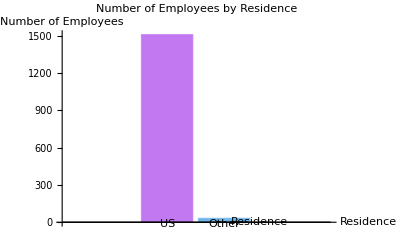

```mathematica
BarChart[Values[residencyCounts],ChartLabels->Keys[residencyCounts],PlotLabel->"Number of Employees by Residence",AxesLabel->{"Residence","Number of Employees"},ChartStyle->"Pastel"]
```

```mathematica
(*Visualizing the Jobs in terms of the type of contract*)
```

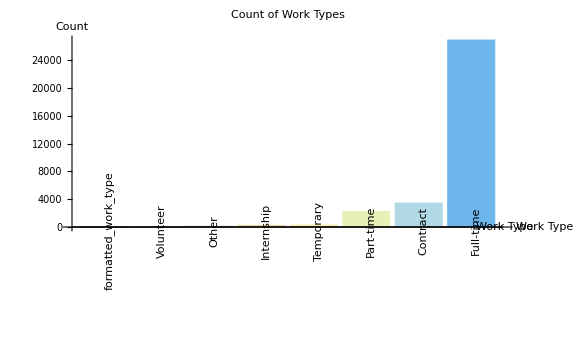

<||>

```mathematica
formattedWorkTypeCol=10; 
workTypeTally=Tally[JobPosting[[All,formattedWorkTypeCol]]];

sortedWorkTypeTally=SortBy[workTypeTally,Last];

BarChart[Last/@sortedWorkTypeTally,ChartLabels->Placed[First/@sortedWorkTypeTally,Below,Rotate[#,Pi/2]&],PlotLabel->"Count of Work Types",AxesLabel->{"Work Type","Count"},ChartStyle->"Pastel",ImageSize->Large]
```